# 3 - D Woods-Saxon

```mathematica
V[r]==V0/(1+Exp[-(r-R0)/a]) (* for 0<x^2+y^2+z^2<a^2 )
```

```mathematica
(* the schrodinger equation is *)
(-ℏ^2/(2m)∇^2 +V[r])ψ[r,θ,ϕ]== Ε ψ[r,θ,ϕ]
```

```mathematica
(* seperating varible *)
ψ[r,θ,ϕ] ==R[r]Y[l,m,θ,ϕ]
```

```mathematica
(1/r^2∂/(∂r)(r^2∂/(∂r))-1/r^2 L^2 - (2m)/ℏ^2 V[r])R[r]Y[l,m,θ,ϕ]==-(2m Ε)/ℏ^2 R[r]Y[l,m,θ,ϕ]
```

```mathematica
(* we have decoupled equation *)
(1/r^2 ⅆ/ⅆr(r^2 ⅆ/ⅆr)-(l(l+1))/r^2- (2m)/ℏ^2 V[r])R[r]==-(2m Ε)/ℏ^2 R[r]
L^2 Y[l,m,θ,ϕ]== l(l+1) Y[l,m,θ,ϕ]
```

```mathematica
Y[l_,m_,θ_,ϕ_]:=SphericalHarmonicY[l,m,θ,ϕ]
```

```mathematica
(* the solution of the radial part is *)
(1/r^2 ⅆ/ⅆr(r^2 ⅆ/ⅆr)-(l(l+1))/r^2- (2m)/ℏ^2 V[r])R[r]==-(2m Ε)/ℏ^2 R[r]
```

```mathematica
r^2(ⅆ^2 R)/(ⅆ r^2)+ 2 r ⅆR/ⅆr+( k^2 r^2-l(l+1)- (2m)/ℏ^2 r^2 V[r])R[r]==0
(* insert k = √((2mE)/ℏ^2) becomes *)
(kr)^2(ⅆ^2 R)/(ⅆ(kr)^2)+ 2 (kr) ⅆR/(ⅆ(kr))+( (kr)^2-l(l+1)- (kr)^2/Ε V[r])R[r]==0
(* change x = kr *)
x^2(ⅆ^2 R)/(ⅆ x^2)+ 2 x ⅆR/ⅆx+( x^2-l(l+1)- x^2/Ε V[x/k])R[x/k]==0
```

## V = 0

```mathematica
x^2(ⅆ^2 R)/(ⅆ x^2)+ 2 x ⅆR/ⅆx+( x^2-l(l+1))R[x/k]==0
```

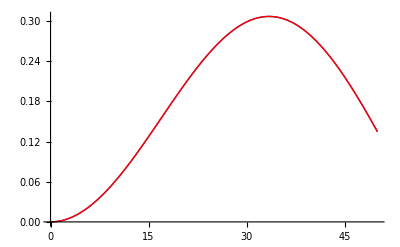

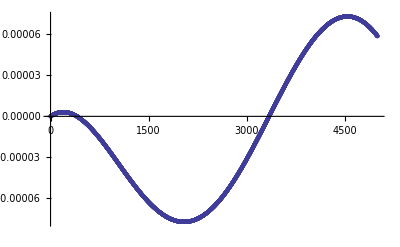

```mathematica
R0={0.01,1,0};
h=0.01;
l=2;
n=5000;
k=0.1;
α=1;
Array[U,n];
U[1]=R0;
Table[temp=U[i-1];
U[i]={temp[[1]]+h ,
h temp[[3]]+temp[[2]],
 temp[[3]]-h/temp[[1]]^2(2 temp[[1]]temp[[3]]+((k temp[[1]])^2-l(l+1))temp[[2]])},{i,2,n}];
Rs=Table[{U[i][[1]],SphericalBesselJ[l,k U[i][[1]]]},{i,1,n}];
maxRs=Max[Table[Rs[[i,2]],{i,1,n}]];
maxR=Max[Table[U[i][[2]],{i,1,n}]];
R=Table[{U[i][[1]],U[i][[2]] maxRs/maxR α},{i,1,n}];
Show[
ListPlot[R,Joined->True,PlotRange->All],
Plot[SphericalBesselJ[l,k x],{x,0,R0[[1]]+h n},PlotStyle->Red,PlotRange->All]
]

ListPlot[Table[R[[i,2]]-Rs[[i,2]],{i,1,n}]]
```

## V = Vls L s

```mathematica
x^2(ⅆ^2 R)/(ⅆ x^2)+ 2 x ⅆR/ⅆx+( x^2+l(l+1)+Vls)R[x/k]==0
```

```mathematica
V[Vls_,j_,l_]:=Vls (j(j+1)-l(l+1)-3/4)/2
```

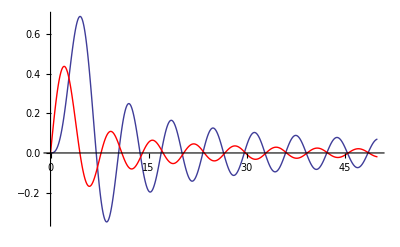

```mathematica
R0={0.001,0,0.1};
h=0.01;
l=1;
j=1/2;
Vls =10;
n=5000;
α=-0.0001;
Array[U,n];
U[1]=R0;
Table[temp=U[i-1];
U[i]={temp[[1]]+h ,
h temp[[3]]+temp[[2]],
 temp[[3]]-h/temp[[1]]^2(2 temp[[1]]temp[[3]]+((k temp[[1]])^2-l(l+1))temp[[2]]) },{i,2,n}];
R=Table[{U[i][[1]],U[i][[2]] α},{i,1,n}];
Show[
ListPlot[R,Joined->True,PlotRange->All],
Plot[SphericalBesselJ[l,k x],{x,0,R0[[1]]+h n},PlotStyle->Red,PlotRange->All]
]
```

## V = Woods-Saxon

```mathematica
r^2(ⅆ^2 R)/(ⅆ r^2)+ 2 r ⅆR/ⅆr+( (2mp E)/ℏ^2 r^2-l(l+1)- (2mp)/ℏ^2 r^2 V[r])R[r]==0
```

```mathematica
Vws[V0_,r_,R0_,a0_]:=V0/(1+Exp[(r-R0)/a0])
```

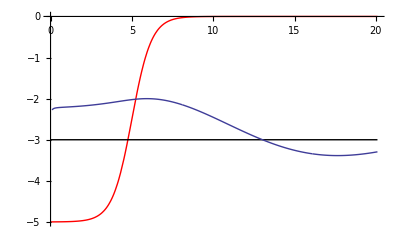

```mathematica
R0={0.1,1,1};
h=0.001;
l=0;
n=20000;
k=0.3;
V0=-5;
energy=-3;
r0=5;
a0=0.6;
Array[U,n];
U[1]=R0;
Table[temp=U[i-1];
U[i]={temp[[1]]+h ,
h temp[[3]]+temp[[2]],
 temp[[3]]-h/temp[[1]]^2(2 temp[[1]]temp[[3]]+((k temp[[1]])^2-l(l+1)-(k temp[[1]])^2/energy Vws[V0,temp[[1]],r0,a0])temp[[2]]) },{i,2,n}];
maxR=Max[Table[U[i][[2]],{i,1,n}]];
R=Table[{U[i][[1]],(U[i][[2]])/maxR+energy},{i,1,n}];
Show[
Plot[{Vws[V0,r,r0,a0],energy},{r,0,R0[[1]]+h n},PlotStyle->{Red,Black},PlotRange->All],
ListPlot[R,Joined->True,PlotRange->All]
]
```